# Careful with := vs =

This is not a trivial mistake. When defines is used, the transpose formed during the table draws from the smooth kernel distribution twice, and these samples drawn are DIFFERENT! That is the problem. I proved that they are different by realising a zero correlation despite using a 100% pure linear straight line that was intended for analysis.

https://twitter.com/datepsych/status/1741677937038913931 
Turns out the problem is not the noise, it is the design set up. There are too few bins!

You derive an smooth kernel distribution or probability distribution from the bins, it is Gaussian. Now actually use that distribution, the correlation washes out.

-Graphics-

Use the coefficients.  
What does /. mean?
It means replace values.

Note that Wolfram Engine is stringent to *

Claim is made for coefficient to be robustly is zero.

```mathematica
?/.
```

Replicate the table, how is the table replicated?

```mathematica
X=Table[i,{i,1,7,1}]
```

{1,2,3,4,5,6,7}

We do not have the total sample count. In reality, I suspect only 32 surveys were done. Time to multiply the sample count by 100.

```mathematica
Y={2,2,5, 8, 9, 4, 2}
```

{2,2,5,8,9,4,2}

```mathematica
ta=Table[Table[X[[i]],{Y[[i]]}],{i,1,Length[X]}]//Flatten;
```

Makes the distribution into an empirical distribution. I doubt that there are actually 32 points.

```mathematica
dist=EmpiricalDistribution[ta]
```

DataDistribution[…]

From a power law discussion, the square of a variable has half the tail exponent.

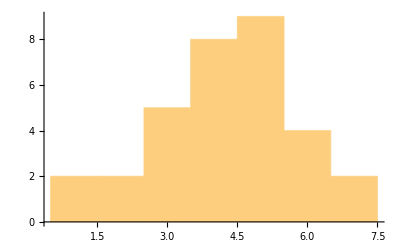

```mathematica
Histogram[ta]
```

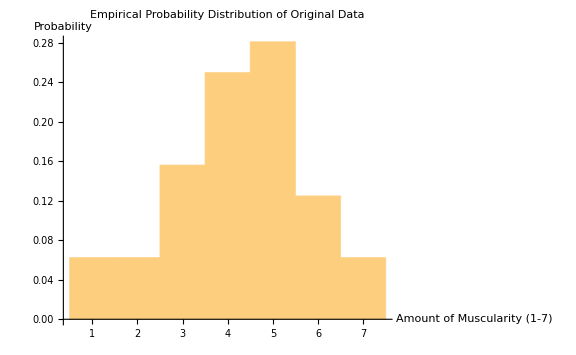

```mathematica
Histogram[ta,10,Probability,PlotLabel->"Empirical Probability Distribution of Original Data",AxesLabel->{"Amount of Muscularity (1-7)","Probability"},ImageSize->Large]
```

This is the key step in replicating the paper. Take the smooth kernel distribution. It makes the distribution of the bins smoother.

```mathematica
dist2=SmoothKernelDistribution[ta];
```

Apply N to all these values which makes them real and not fractions.

```mathematica
{Mean[dist2],Kurtosis[dist2],Skewness[dist2]}//N
```

{4.25,2.8088,-0.242821}

```mathematica
{Skewness[ta],Skewness[dist2]}//N
```

{-0.319444,-0.242821}

Muscularity of individuals apparently follow a normal distribution

### Monte-Carlo of both the distribution and the quadratic term.

I FOUND AN ERROR IN TALEB’S METHOD OF DOING THIS. Define “:=” causes the transpose to take on two different probability distributions, one for ta3 and the other for the function f. The correct syntax should be normal =.
https://www.youtube.com/watch?v=0z4ZfRdxErA

You see in here, he used := to define the ta, this guarantees that the two tables generated will be different. He should be using = instead. NOTE: for this example I forced zero Gaussian noise instead.

```mathematica
ta3=RandomVariate[dist2,Length[f1]];
ff=a*x+b/.{a->1,b->30};
f2=ff/.x->ta3;
reg3:=Transpose[{ta3,f2}]
```

```mathematica
ta3
```

{7.00907,2.93311,3.49844,4.05632,4.29589,3.63592,5.60169,1.40346,3.5149,4.82233,1.64115,2.90217,6.12029,5.33306,2.48681,3.74212,4.97234,3.52999,3.82176,4.5401,5.76483,1.04623,7.17876,1.47959,3.01171,2.01656,1.45028,2.2311,6.18441,3.88613,4.88231,3.04267}

```mathematica
reg3
```

{{7.00907,37.0091},{2.93311,32.9331},{3.49844,33.4984},{4.05632,34.0563},{4.29589,34.2959},{3.63592,33.6359},{5.60169,35.6017},{1.40346,31.4035},{3.5149,33.5149},{4.82233,34.8223},{1.64115,31.6411},{2.90217,32.9022},{6.12029,36.1203},{5.33306,35.3331},{2.48681,32.4868},{3.74212,33.7421},{4.97234,34.9723},{3.52999,33.53},{3.82176,33.8218},{4.5401,34.5401},{5.76483,35.7648},{1.04623,31.0462},{7.17876,37.1788},{1.47959,31.4796},{3.01171,33.0117},{2.01656,32.0166},{1.45028,31.4503},{2.2311,32.2311},{6.18441,36.1844},{3.88613,33.8861},{4.88231,34.8823},{3.04267,33.0427}}

Versus here:

```mathematica
ta3:=RandomVariate[dist2,Length[f1]];
ff=a*x+b/.{a->1,b->30};
f2=ff/.x->ta3;
reg3:=Transpose[{RandomVariate[dist2,Length[f1]],f2}]
```

```mathematica
ta3
```

{4.12877,5.443,4.64067,5.61032,6.69105,4.00235,6.22784,3.55072,3.90544,4.72391,2.86448,6.2811,6.29252,3.41009,5.63359,4.9597,5.54287,3.38915,4.78762,7.25406,4.87465,5.2594,5.89717,6.74191,3.8394,1.58911,6.93017,5.59537,4.94935,4.68708,1.16846,4.10253}

```mathematica
reg3
```

{{4.27978,34.2567},{5.47935,32.6424},{5.94517,33.9881},{5.8043,35.5792},{8.08404,34.176},{1.36074,37.0521},{4.58998,32.843},{7.36355,36.483},{8.03468,35.4928},{1.97068,33.6719},{5.37758,30.847},{1.90427,35.5974},{4.02022,34.6105},{6.28528,32.3273},{2.96934,37.736},{0.809693,34.4555},{2.98022,35.652},{6.82761,37.1839},{4.6079,33.0047},{3.94344,34.7458},{2.88582,34.3134},{5.81835,34.9801},{5.1014,34.2108},{1.82026,35.6695},{4.38448,34.645},{3.53723,32.4112},{3.43139,34.7503},{5.11773,31.4009},{3.34238,34.4506},{6.64329,32.8818},{3.3289,31.8397},{5.68225,32.0083}}

```mathematica
ta3=Table[lm3=LinearModelFit[reg3,{1,x},x];lm3[x][[2]][[1]],{z,1,10^3}];
```

```mathematica
{Mean[ta3],StandardDeviation[ta3],Kurtosis[ta3]}
```

{1.,0.,Indeterminate}

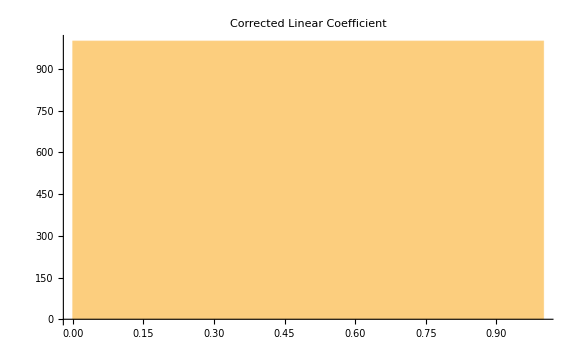

```mathematica
pl2=Histogram[ta3,PlotLabel->"Corrected Linear Coefficient",ImageSize->Large]
```